A tensor network is a graph annotated with tensors and contraction indices. A quantum circuit can be understood as a tensor network, where each gate is replaced by corresponding tensor, and edges represents corresponding index contractions. In this short computational essay, we explore tensor networks in the Wolfram quantum framework, and discuss how it provides a more efficient way to do computations.

Wolfram Quantum Team (quantum AT wolfram.com)

## Paclet installation

Install Wolfram quantum paclet:

```mathematica
PacletInstall["Wolfram/QuantumFramework"]
Needs["Wolfram`QuantumFramework`"]
```

PacletObject[…]

One can also use the developer link to install the paclet; which is updated more often (eg daily) compared to the paclet link above:
PacletInstall["https://wolfr.am/DevWQCF",ForceVersionInstall->True]

## Tensor networks

Create a quantum circuit:

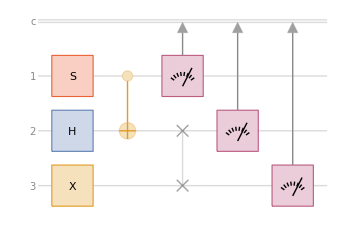

```mathematica
circuit=QuantumCircuitOperator[{"S","H"->2,"X"->3,"CNOT","SWAP"->{2,3},{1},{2},{3}}];
circuit["Diagram"]
```

Note in Wolfram quantum framework, each measurement result is saved in an ancillary quantum system (call it a detector, for example). So the true diagram will be something like this:

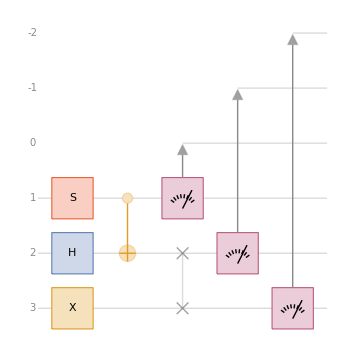

```mathematica
circuit["Diagram","ShowExtraQudits"->True]
```

Note the first measurement is saved in the wire labeled as 0 and the rest goes backward, with negative labels.

Return the tensor network representation of the circuit:

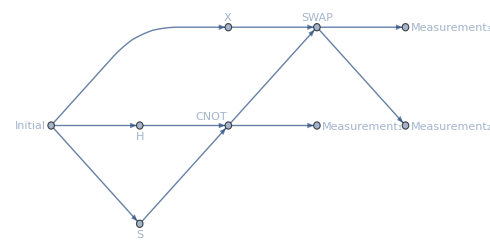

```mathematica
net=circuit["TensorNetwork",GraphLayout -> {"LayeredDigraphEmbedding", "Orientation" -> Left}]
```

The tensor network is a graph annotated with tensors and contraction indices.

```mathematica
GraphQ[net]&&TensorNetworkQ[net]
```

True

Lists all annotation keys available for the tensor network:

```mathematica
AnnotationKeys[{net,0}]
```

{Index,Tensor,VertexCoordinates,VertexLabels,VertexShape,VertexShapeFunction,VertexSize,VertexStyle}

Let’s look at tensor, vertex labels, and corresponding indexes in the tensor network:

```mathematica
list=Developer`FromPackedArray@VertexList[net];
TableForm[Transpose[Prepend[AnnotationValue[{net,list},#]&/@{"Tensor","Index"},Sort@AnnotationValue[net,VertexLabels]]],]
```

VertexLabel | Tensor | Index
0→Initial | SparseArray[…] | {0^1,0^2,0^3}
1→S | SparseArray[…] | {1^1,1_1}
2→H | SparseArray[…] | {2^2,2_2}
3→X | SparseArray[…] | {3^3,3_3}
4→CNOT | SparseArray[…] | {4^1,4^2,4_1,4_2}
5→SWAP | SparseArray[…] | {5^2,5^3,5_2,5_3}
6→Measurement_1 | SparseArray[…] | {6^0,6^1,6_1}
7→Measurement_2 | SparseArray[…] | {7^-1,7^2,7_2}
8→Measurement_3 | SparseArray[…] | {8^-2,8^3,8_3}

Note tensors in the tensor network are mixed type, meaning they consist of so-called “contravariant” (upper) indices and “covariant” (lower) indices. For example, the 2nd measurement (7th vertex), acts on qubit-2 (denoted by contravariant and covariant indices 2) and its result is saved on wire, denoted by the index “-1”.

Vertices correspond to circuit’s operators/gate indices, in addition to “Initial” tensor with index 0 (for the initial state):

```mathematica
VertexList[net]
```

{0,1,2,3,4,5,6,7,8}

```mathematica
Length@circuit["Flatten"]["Operators"]
```

8

```mathematica
%==Max[%%]
```

True

Note that each edge represents (i.e., is tagged by) a contraction:

```mathematica
EdgeList[net]
```

{01{0^1,1_1},02{0^2,2_2},03{0^3,3_3},14{1^1,4_1},24{2^2,4_2},45{4^2,5_2},35{3^3,5_3},46{4^1,6_1},57{5^2,7_2},58{5^3,8_3}}

Perform the contraction:

```mathematica
finalTensor=ContractTensorNetwork[net]
```

SparseArray[…]

Confirm that the result is the same as default circuit application:

```mathematica
circuit[]["Tensor"]==finalTensor
```

True

Another tensor network representation uses indices as graph vertices with tensors as cliques:

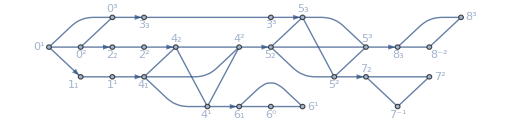

```mathematica
indexNet=TensorNetworkIndexGraph[net,GraphLayout -> {"LayeredDigraphEmbedding", "Orientation" -> Left}]
```

Note in above graph, the directed edges imply tensor contraction; also tensors are cliques in above graph

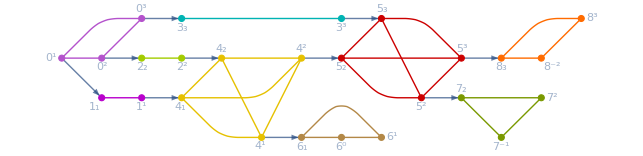

```mathematica
HighlightGraph[indexNet,Subgraph[indexNet,#]&/@FindClique[indexNet,Infinity,All]]
```

Free indices are the ones that left after contraction:

```mathematica
TensorNetworkFreeIndices[net]
```

{8^-2,7^-1,6^0,6^1,7^2,8^3}

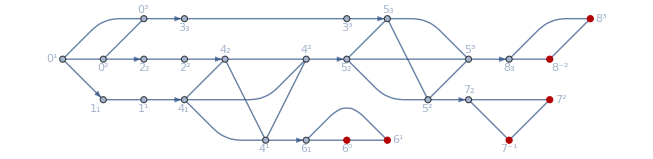

```mathematica
HighlightGraph[indexNet,TensorNetworkFreeIndices[net]]
```

Free indices can be extracted as vertices with zero in- and out- degree:

```mathematica
Pick[VertexList[indexNet],VertexInDegree[indexNet]+VertexOutDegree[indexNet],0]
```

{6^0,6^1,7^-1,7^2,8^-2,8^3}

```mathematica
ContainsExactly[TensorNetworkFreeIndices[net],TensorNetworkFreeIndices[net]]
```

True

### Contraction and Einstein Summation

What ContractTensorNetwork does is in fact  EinsteinSummation.

```mathematica
indices=AnnotationValue[{net,list},"Index"]/.Rule@@@EdgeTags[net]
out=TensorNetworkFreeIndices[net]
tensors=AnnotationValue[{net,list},"Tensor"];
```

{{1_1,2_2,3_3},{4_1,1_1},{4_2,2_2},{5_3,3_3},{6_1,5_2,4_1,4_2},{7_2,8_3,5_2,5_3},{6^0,6^1,6_1},{7^-1,7^2,7_2},{8^-2,8^3,8_3}}

{8^-2,7^-1,6^0,6^1,7^2,8^3}

Show ContractTensorNetwork is the same as EinsteinSummation:

```mathematica
ContractTensorNetwork[net]===ResourceFunction["EinsteinSummation"][indices->out,tensors]
```

True

One can compare the performance, on how the relevant computation is done

Perform the contraction in the order of network’s EdgeList:

```mathematica
ContractTensorNetwork[net,Method->"Naive"];//RepeatedTiming
```

{0.0337542,Null}

Optimize the order for contraction, using EinsteinSummation and symbolic tensors package:

```mathematica
ContractTensorNetwork[net];//RepeatedTiming
```

{0.00261204,Null}

### Initial state different from ground state

Note that the initial tensor in the tensor network we studied here was a registered state. Additionally, one can start from any initial state.

Generate a random state:

```mathematica
ψ0=QuantumState[{"RandomPure",3}];
```

Initialize the tensor network from above state:

```mathematica
net2=Wolfram`QuantumFramework`PackageScope`InitializeTensorNetwork[net,ψ0["Tensor"]];
```

See supplement info, for package-scoped symbols.

Show the tensor contraction is the same as transformation of state by the circuit:

```mathematica
ContractTensorNetwork[net2]==circuit[ψ0]["Tensor"]
```

True

## Supplement info

### Package-scoped symbols

Note in Wolfram quantum framework, there are some package-scoped symbols that live in Wolfram`QuantumFramework`PackageScope` context.

```mathematica
?Wolfram`QuantumFramework`PackageScope`$*
```

### FromTensorNetwork

Any directed graph can be turned into a tensor network, even if the graph is not annotated.

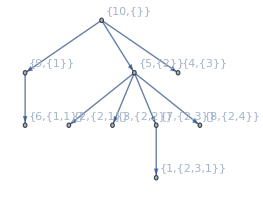

```mathematica
graph=TreeGraph[RandomTree[10],VertexLabels->Automatic]
```

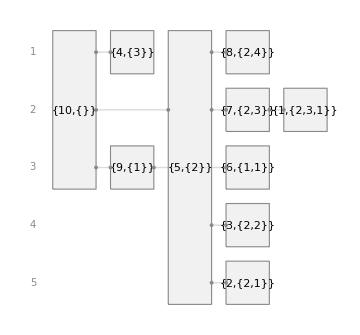

```mathematica
qcTN1=FromTensorNetwork@graph;
qcTN1["Diagram","ShowConnectors"->True]
```

```mathematica
graph2=DirectedGraph[RandomGraph[{10,10}],"Acyclic",VertexLabels->v_:>HoldForm[v]]
```

-Graphics-

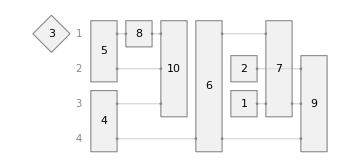

```mathematica
qcTN2=FromTensorNetwork@graph2;
qcTN2["Diagram","ShowConnectors"->True]
```